# Mikroskop

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## 1.1) Gesamtvergrößerung (Okular mit halbdurchlässigen Einblendspiegel)

```mathematica
t= {{140, 145, 150, 155, 160, 165, 170, 175, 180, 185}}*10^-3;
dt = 0;
```

```mathematica
So1 = {{□, □, □, □, □, □, □, □, □, □}};
dso1 = 0;
Sg1 ={{□, □, □, □, □, □, □, □, □, □}};
dsg1 = 0;
```

```mathematica
Vges = Table[Fdiv[Sg1[[1,x]],dsg1,So1[[1,x]],dso1],{x,1,Length[So1[[1]]]}]
```

(1 | 0
1 | 0
1 | 0
1 | 0
1 | 0
1 | 0
1 | 0
1 | 0
1 | 0
1 | 0)

```mathematica
p1 = Table[{{t[[1,x]],Vges[[x,1]]},ErrorBar[dt,Vges[[x,1]]]},{x,1,Length[Vges]}];
```

```mathematica
pp= Table[{t[[1,x]],Vges[[x,1]]},{x,1,Length[Vges]}];
```

```mathematica
pf1=LinearModelFit[pp,x,x]
```

FittedModel[1.-7.74765×10^-15 x]

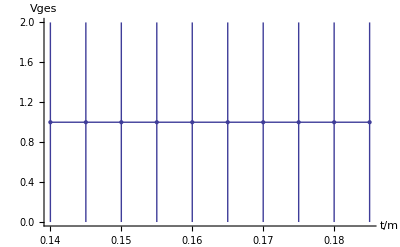

```mathematica
Show[
 ErrorListPlot[p1],
Plot[pf1[x],{x,Min[t],Max[t]}],AxesLabel->{"t/m","Vges"}]
```

```mathematica
pf1["ParameterTable"]
para1 = pf1["ParameterTableEntries"];
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 1. | 1.32267×10^-15 | 7.56045×10^14 | 1.04915×10^-116
x | -7.74765×10^-15 | 8.10792×10^-15 | -0.955565 | 0.367272

```mathematica
xt = {para1[[1,1]],para1[[1,2]]}
```

{1.,1.32267×10^-15}

```mathematica
k={para1[[2,1]],para1[[2,2]]}
```

{-7.74765×10^-15,8.10792×10^-15}

## 1.2) Objektivvergrößerung (Hilfsokular mit Okularmikrometer)

```mathematica
Sok = {{□, □, □, □, □, □, □, □, □, □}};
dsok = 0;
Sg2 = {{□, □, □, □, □, □, □, □, □, □}};
dsg2 = 0;
```

```mathematica
Vobj = Table[Fdiv[Sok[[1,x]],dsok,Sg2[[1,x]],dsg2],{x,1,Length[Sok[[1]]]}];
```

## 2.) Okularvergrößerung

```mathematica
Vokt = Table[Fdiv[Vges[[x,1]],Vges[[x,2]],Vobj[[x,1]],Vobj[[x,2]]],{x,1,Length[Sok[[1]]]}];
```

```mathematica
Vok = Gauss[Vokut[[1;;Length[Vokut],1]]]
```

{1,0}

## 3) Objektivbrennweite

```mathematica
vgr = Table[Fmult[k[[1]],k[[2]],t[[1,x]],dt],{x,1,Length[t[[1]]]}]
```

(-1.08467×10^-15 | 1.13511×10^-15
-1.12341×10^-15 | 1.17565×10^-15
-1.16215×10^-15 | 1.21619×10^-15
-1.20089×10^-15 | 1.25673×10^-15
-1.23962×10^-15 | 1.29727×10^-15
-1.27836×10^-15 | 1.33781×10^-15
-1.3171×10^-15 | 1.37835×10^-15
-1.35584×10^-15 | 1.41889×10^-15
-1.39458×10^-15 | 1.45943×10^-15
-1.43331×10^-15 | 1.49997×10^-15)

```mathematica
fobjt = Table[Ff[t[[1,x]]-xt[[1]],dt+xt[[2]],Vok[[1]],Vok[[2]],vgr[[x,1]],vgr[[x,2]]],{x,1,Length[t[[1]]]}]
```

(7.92867×10^14 | 8.29737×10^14
7.61076×10^14 | 7.96467×10^14
7.31405×10^14 | 7.65416×10^14
7.03647×10^14 | 7.36368×10^14
6.77625×10^14 | 7.09135×10^14
6.5318×10^14 | 6.83553×10^14
6.30172×10^14 | 6.59476×10^14
6.0848×10^14 | 6.36775×10^14
5.87992×10^14 | 6.15334×10^14
5.68612×10^14 | 5.95053×10^14)

```mathematica
fobj = Gauss[fobjt[[1;;Length[fobjt],1]]]
```

{6.71506×10^14,2.3802×10^13}

## 4) Okularbrennweite

```mathematica
s0 = 25*10^-2;
ds0 = 0;
```

```mathematica
fok = Fdiv[s0,ds0,Vok[[1]],Vok[[2]]]
```

{1/4,0}

## 5) Gesamtbrennweite

```mathematica
fges = Table[Ff[fobj[[1]],fobj[[2]],fok[[1]],fok[[2]],t[[1,x]]-xt[[1]],dt+xt[[2]]],{x,1,Length [t[[1]]]}]
```

(-1.95205×10^14 | 6.91919×10^12
-1.96347×10^14 | 6.95965×10^12
-1.97502×10^14 | 7.00059×10^12
-1.9867×10^14 | 7.04202×10^12
-1.99853×10^14 | 7.08393×10^12
-2.0105×10^14 | 7.12635×10^12
-2.02261×10^14 | 7.16928×10^12
-2.03487×10^14 | 7.21273×10^12
-2.04727×10^14 | 7.25671×10^12
-2.05983×10^14 | 7.30123×10^12)